# DRS - “Pod-Rocker” mechanism (b)

## Kinematic analysis

```mathematica
data = {L1->20, L2->20, L3 ->50, L4 -> 40, α ->80*Pi/180, xP1 ->40, yP1->-20,  yP4->20};
```

```mathematica
P0 = {s,0};
P1 = {xP1, yP1}/.data;
P2a = {s+L1, 0}/.data;
P2b = {xP1 + L2*Cos[th1+α], 0}/.data;
P4a = {xP4, yP4}/.data;
```

```mathematica
kinsol = Solve[P2a == P2b, th1][[2]]/.C[1]->0
```

{th1→1/18 (π-18 ArcSin[1/20 (-20+s)])}

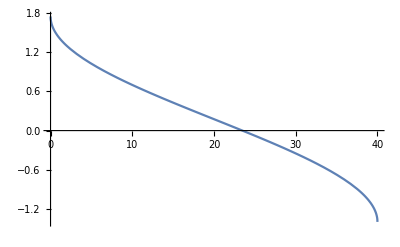

```mathematica
Plot[{th1/.kinsol},{s,0,40}]
```

```mathematica
P2 = {s+L1, 0}/.data;
P3 = {xP1 + L3 * Cos[th1], yP1 + L3 * Sin[th1]}/.data/.kinsol;
```

```mathematica
Manipulate[
Show[
ListPlot[{P0,P2}/.s->S,Joined->True,PlotStyle->{Red,Thick}, PlotRange->{{-30,120},{-30,120}},AspectRatio->1],
ListPlot[{P2,P1}/.s->S,Joined->True,PlotStyle->{Blue,Thick}],
ListPlot[{P3,P1}/.s->S,Joined->True,PlotStyle->{Blue,Thick}],
ListPlot[{P2,P3}/.s->S,Joined->True,PlotStyle->{Blue,Thick}],
ListPlot[{P3,P4}/.s->S,Joined->True,PlotStyle->{Green,Thick}],
Graphics[{Gray,Circle[{xP1/.data,yP1/.data},L2/.data],
Circle[{xP1/.data,yP1/.data},L3/.data],
Circle[{xP4/.data,yP4/.data},L4/.data]
}]
],{S,0,40}]
```